```mathematica
(*In this document was chosen a fcuntion to work with in the next steps and it is define as f(x). Also, was defined the subinterval and its convergence according to the Gaussian Quadrature*)
Needs["NumericalDifferentialEquationAnalysis`"];
```

# Benchmark

```mathematica
p=10; (*Número de pontos*)
d=10; (*10^d Representa a precisão desejada*)
a=-10; (*Menor limite de integração*)
b=10;(*Maior limite de integração*)
e=1; (*espaçemtno*)
```

```mathematica
c5=Table[a+i*e  -e ->  a+i*e ,{i,1,(b-a)*(1/e)}];
```

```mathematica
f[x_]=ArcTan[(x-5)^2];
```

```mathematica
ExactIntegral=Integrate[f[x],{x,a,b}]//N
```

27.2397+0. ⅈ

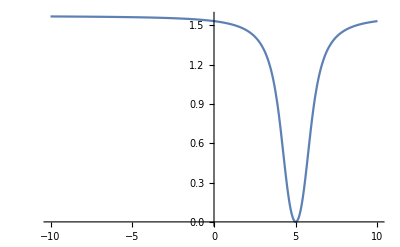

```mathematica
Plot[f[x],{x,a,b},PlotRange->All]
```

## Gauss Quadrature:

### General Method

```mathematica
Gauss[n_,a_,b_]:=Module[{aux,Wivec,fvec, valor},
(*"n" representa o número de pontos de integração*)
aux=SetPrecision[GaussianQuadratureWeights[n,a,b],MachinePrecision];
Wivec=aux[[All,2]];
fvec=f[aux[[All,1]]];
valor=fvec.Wivec;
Return[valor];
];
```

### Dividing the function:

```mathematica
(*Convergência da função f(x)*)
```

```mathematica
Chop[Table[Abs[Gauss[i,a,b]-Integrate[f[x],{x,a,b}]],{i,1,p}],10^-d]
```

{3.37666,6.22615,3.05417,1.37079,3.06606,1.95864,0.171002,1.33273,1.06556,0.0977485}

```mathematica
(*Plotagem da divisão*)
```

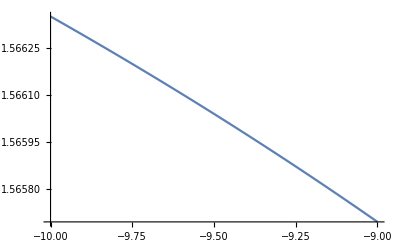
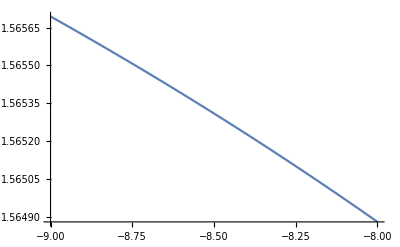
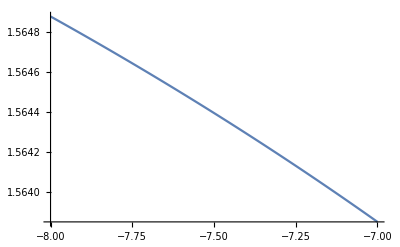
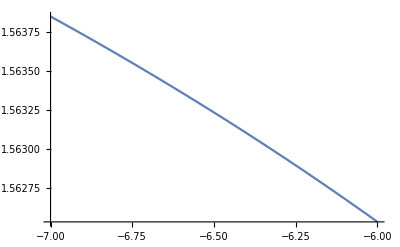
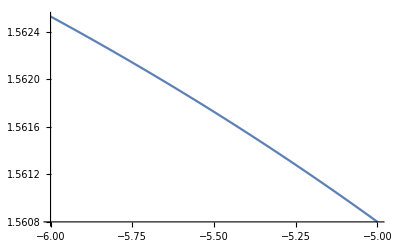
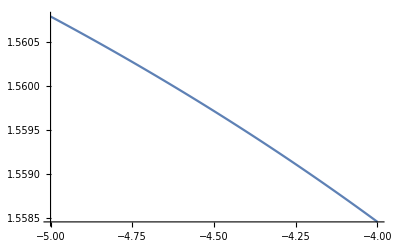
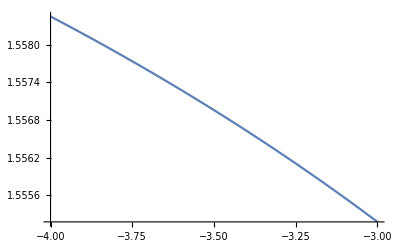
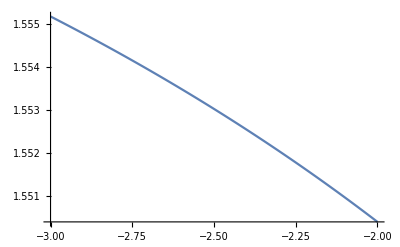

```mathematica
Table[Plot[f[x],{x,(a+i*e)-e,a+i*e}],{i,1,(b-a)*(1/e)}]
```

```mathematica
(*Convergência do método de Gauss para cada segmento da função f(x)*)
```

```mathematica
AbsoluteTiming[Chop[TableForm[Table[Abs[Gauss[n,(a+i*e)-e,a+i*e]-Integrate[f[x],{x,(a+i*e)-e,a+i*e}]],{i,1,(b-a)*(1/e)},{n,1,10}],TableHeadings-> {c5,Automatic}],10^-d]]
```

{119.385, | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
-10→-9 | 5.66189×10^-6 | 2.99412×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-9→-8 | 7.53651×10^-6 | 4.59811×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8→-7 | 0.0000102554 | 7.29873×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7→-6 | 0.000014319 | 1.20412×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6→-5 | 0.0000206103 | 2.07923×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5→-4 | 0.0000307698 | 3.79238×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4→-3 | 0.0000480368 | 7.39582×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3→-2 | 0.0000793059 | 1.56814×10^-7 | 2.50426×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2→-1 | 0.000140698 | 3.70196×10^-7 | 7.84994×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1→0 | 0.000274766 | 1.00796×10^-6 | 2.9665×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0→1 | 0.00061367 | 3.34335×10^-6 | 1.44466×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1→2 | 0.00167308 | 0.0000147347 | 9.90168×10^-8 | 5.41097×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
2→3 | 0.00624341 | 0.0000953018 | 8.63041×10^-7 | 6.27773×10^-10 | 1.50636×10^-10 | 0 | 0 | 0 | 0 | 0
3→4 | 0.0323647 | 0.0000103448 | 0.0000421858 | 1.13089×10^-7 | 7.94243×10^-8 | 2.63205×10^-10 | 1.77185×10^-10 | 0 | 0 | 0
4→5 | 0.052924 | 0.00263421 | 0.000231908 | 0.0000164035 | 9.03098×10^-7 | 2.8266×10^-8 | 1.91183×10^-9 | 4.88865×10^-10 | 0 | 0
5→6 | 0.052924 | 0.00263421 | 0.000231908 | 0.0000164035 | 9.03098×10^-7 | 2.82651×10^-8 | 1.91101×10^-9 | 4.8969×10^-10 | 0 | 0
6→7 | 0.0323647 | 0.0000103448 | 0.0000421858 | 1.1309×10^-7 | 7.94239×10^-8 | 2.62744×10^-10 | 1.77646×10^-10 | 0 | 0 | 0
7→8 | 0.00624341 | 0.0000953018 | 8.63041×10^-7 | 6.27605×10^-10 | 1.50805×10^-10 | 0 | 0 | 0 | 0 | 0
8→9 | 0.00167308 | 0.0000147347 | 9.90167×10^-8 | 5.40983×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
9→10 | 0.00061367 | 3.34335×10^-6 | 1.44465×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0}